```mathematica
SetDirectory[NotebookDirectory[]];
```

#### 3.1.2 Continuous Formulation and Berry Phase

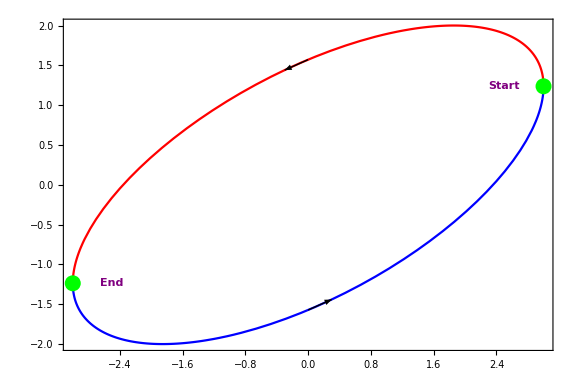

```mathematica
p1=ParametricPlot[{3Cos[t],2Sin[t+2/3]},{t,0,Pi},ImageSize->Large,PlotStyle->Red];
p2=ParametricPlot[{3Cos[t],2Sin[t+2/3]},{t,Pi,2Pi},ImageSize->Large,PlotStyle->Blue];
p3=Graphics[{PointSize[0.02],Green,Point[{{3Cos[0],2Sin[0+2/3]},{3Cos[Pi],2Sin[Pi+2/3]}}]}];
p4=Graphics[{Arrow[{tant[t]/.t->0.0,tant[t]/.t->0.1}],Arrow[{tant[t]/.t->0.0+Pi,tant[t]/.t->0.1+Pi}]}];
p5=Graphics[{Text[Style["Start",Large,Bold,Purple],{3Cos[0]-0.5,2Sin[0+2/3]}],Text[Style["End",Large,Bold,Purple],{3Cos[Pi]+0.5,2Sin[Pi+2/3]}]}];
tant[t_]:=D[{3Cos[t],2Sin[t+2/3]},t]
Show[{p1,p2,p3,p4,p5},Frame->True,PlotRange->All,ImageSize->Large,FrameStyle->Directive[Bold,Large]]
```

```mathematica
Manipulate[ParametricPlot3D[{Sinc[a u] u,v,1/a-Cos[a u]/a},{u,0,2 Pi},{v,0,2 Pi},ImageSize->Large,Mesh->{{0.}},MeshFunctions->{#4-#5&},MeshStyle->Red,BoxRatios->{3 π,2 π,4},PlotRange->{{-π,2 π},{0,2 π},{0,4}},PlotStyle->Directive[Green,Opacity[0.3],Specularity[White,50]],ViewPoint->{0,1,-2},ViewVertical->{0,1,0},BoundaryStyle->Directive[Black,Opacity[.3]]],{{a,.01,"wrap"},0.001,1}]
```

#### 3.1.3 Example

```mathematica
imag=Import["Spherical.png"]
```

-Graphics-

```mathematica
ra=1.0;
rb=ra+0.2;
ϕ=Pi/4;
range=Pi;
p1=Graphics3D[{Opacity[0.5],Sphere[{0,0,0},ra]}];
arr[ϕ_,θ_]:=Graphics3D[Arrow[{{0,0,0},{rb Sin[ϕ]Cos[θ],rb Sin[ϕ]Sin[θ],rb Cos[ϕ]}}]];(*可以通过rb设置球半径*)
arr2[ϕ_,θ_]:=Graphics3D[Arrow[{{0,0,0},{Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}}]];(*箭头位置指向,这是球半径默认为1的位置*)
pt[ϕ_,θ_]:=Graphics3D[Point[{{0,0,0},{Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}}]];
pts[ϕ_,θ_]:={Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}
a1=Table[pts[ϕ,a],{a,0.,Pi,0.01}];(*路径*)
a1/.{x_,y___}:>{x,y,x};(*路径闭合*)
p2=Graphics3D[{Red,Thickness[0.01],Line[a1]}];
a2=Table[pts[a,ϕ],{a,0.,2Pi,0.01}];(*路径*)
a2/.{x_,y___}:>{x,y,x};(*路径闭合*)
p3=Graphics3D[{Red,Thickness[0.01],Line[a2]}];
Manipulate[Show[{p1,arr2[ϕ,a],p2},ImageSize->Large],{a,0,Pi,0.01}]
```

```mathematica
Manipulate[Show[{p1,arr2[a,ϕ],p3},ImageSize->Large],{a,0,2Pi,0.01}]
```

## Add Magnetic Field(x--->y)

```mathematica
(*直角坐标建立*)
car=Graphics3D[{Blue,Thickness[0.01],Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}]}];


ra = 1.0;
sphere1 = Graphics3D[{Opacity[0.5],Sphere[{0,0,0},ra]}];
coor[ϕ_,θ_]:={Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}(*利用球坐标确定三维空间中的点*)
line1[ϕ_]:=Table[coor[ϕ,θ],{θ,0.,Pi/2,0.01}];(*路径*)
line2[θ_]:=Table[coor[ϕ,θ],{ϕ,0.,Pi/2,0.01}];(*路径*)
a1xy = line2[π/2];
a1xy/.{x_,y___}:>{x,y,x};(*路径闭合*)
Linexy = Graphics3D[{Red,Thickness[0.01],Line[a1xy]}];
arrow[ϕ_,θ_]:=Graphics3D[{Thickness[0.01],Arrow[{{0,0,0},{Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}}]}]
Manipulate[Show[{car,sphere1,Linexy,arrow[ϕ,π/2]},ImageSize->Large],{ϕ,0,π/2,0.01}]
```

## Add Magnetic Field(y---->z)

```mathematica
(*直角坐标建立*)
car=Graphics3D[{Blue,Thickness[0.01],Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}]}];

ra = 1.0;
sphere1 = Graphics3D[{Opacity[0.5],Sphere[{0,0,0},ra]}];
coor[ϕ_,θ_]:={Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}(*利用球坐标确定三维空间中的点*)
line1[ϕ_]:=Table[coor[ϕ,θ],{θ,π/2,0,-0.01}];(*路径*)
line2[θ_]:=Table[coor[ϕ,θ],{ϕ,0.,Pi/2,0.01}];(*路径*)
a1yz = line1[π/2];
a1yz/.{x_,y___}:>{x,y,x};(*路径闭合*)
Lineyz = Graphics3D[{Red,Thickness[0.01],Line[a1yz]}];
arrow[ϕ_,θ_]:=Graphics3D[{Thickness[0.01],Arrow[{{0,0,0},{Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}}]}]
Manipulate[Show[{car,sphere1,Lineyz,arrow[π/2,ϕ]},ImageSize->Large,Framed->False],{ϕ,π/2,0,-0.01}]
```

## General

```mathematica
(*直角坐标建立*)
car=Graphics3D[{Blue,Thickness[0.01],Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}]}];
sphere1 = Graphics3D[{Opacity[0.5],Sphere[{0,0,0},1]}];
coor[ϕ_,θ_]:={Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}(*利用球坐标确定三维空间中的点*)
arrow[ϕ_,θ_]:=Graphics3D[{Thickness[0.01],Arrow[{{0,0,0},coor[ϕ,θ]}]}]
Manipulate[Show[{arrow[ϕ,θ],sphere1}],{ϕ,0,2Pi},{θ,0,2Pi}]
```

## 3.3.2 Chern Theorem

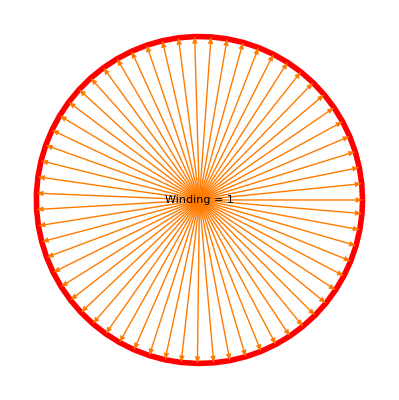

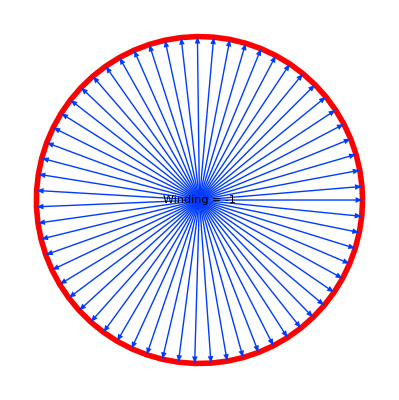

```mathematica
pt1[ϕ_]:={Re@Exp[I ϕ],Im[Exp[I ϕ]]}
pt2[ϕ_]:={Re@Exp[-I ϕ],Im[Exp[-I ϕ]]}
ar1[ϕ_]:={{0,0},pt1[ϕ]}
ar2[ϕ_]:={{0,0},pt2[ϕ]}
arp1=Table[ar1[ϕ],{ϕ,0,2Pi,0.1}];
ro1=Table[pt1[ϕ],{ϕ,0,2Pi,0.1}]/.{p1_,pn___}:>{p1,pn,p1};(*最后利用模式匹配将首尾连接起来*)
ro2=Table[pt2[ϕ],{ϕ,0,2Pi,0.1}]/.{p1_,pn___}:>{p1,pn,p1};
arp2=Table[ar2[ϕ],{ϕ,0,2Pi,0.1}];
line1=Line[ro1];
wind1=WindingCount[line1,{0,0}];
wind2=WindingCount[line2,{0,0}];
line2=Line[ro2];
vor1=Graphics[{{Hue[Random[]],Arrow[arp1]},{Red,Thickness[0.01],Arrow[ro1]},{Text[Style[StringJoin["Winding = ",ToString@wind1],Large],{0,0}]}}]

vor2=Graphics[{{Hue[Random[]],Arrow[arp2]},{Red,Thickness[0.01],Arrow[ro2]},{Text[Style[StringJoin["Winding = ",ToString@wind2],Large],{0,0}]}}]
```